```mathematica
(*f(Subscript[x, 1],...,Subscript[x, d])=Subscript[x, 1],...,Subscript[x, d]*)
(*I=∫_([0,1]^d) f(x)ⅆx = (∫...∫)_([0,1]^d)f(Subscript[x, 1],...,Subscript[x, d])ⅆ Subscript[x, 1]...ⅆ Subscript[x, d]=∫_0^1 (Subscript[x, 1])^2 ⅆ Subscript[x, 1]∫_0^1 Subscript[x, 2] ⅆ Subscript[x, 2]....∫_0^1 Subscript[x, d] ⅆ Subscript[x, d]*)
(*∫_0^1 Subscript[x, i] ⅆ Subscript[x, i]=1/2 (i=2,...,d)& ∫_0^1 Subscript[x, 1]^2 ⅆ Subscript[x, 1]=1/3 => I = 1/3 1/2^(d-1)*)
d=3;
RINT=1/3*1/2^(d-1);
Print["Значение интеграла: ", N[RINT]];
(*I=∫_([0,1]^d) f(x)ⅆx = ∑_(Subscript[j, 1],Subscript[j, 2],...,Subscript[j, d]=1)^m f((2 Subscript[j, 1]-1)/(2m),(2 Subscript[j, 2]-1)/(2m),...,(2 Subscript[j, d]-1)/(2m))=∑_(Subscript[j, 1],Subscript[j, 2],...,Subscript[j, d]=1)^m (((2 Subscript[j, 1]-1)/(2m))^2*(2 Subscript[j, 2]-1)/(2m)*...*(2 Subscript[j, d]-1)/(2m))=∑_(Subscript[j, 2],...,Subscript[j, d]=1)^m ((∑_(Subscript[j, 1]=)^m ((2 Subscript[j, 1]-1)/(2m))^2)*(2 Subscript[j, 2]-1)/(2m)*...*(2 Subscript[j, d]-1)/(2m))=∑_(Subscript[j, 3],...,Subscript[j, d]=1)^m ((∑_(Subscript[j, 1]=)^m ((2 Subscript[j, 1]-1)/(2m))^2)*∑_(Subscript[j, 2]=1)^m ((2 Subscript[j, 2]-1)/(2m))*...*(2 Subscript[j, d]-1)/(2m))=...= 
=∑_(Subscript[j, 1]=)^m ((2 Subscript[j, 1]-1)/(2m))^2*∑_(Subscript[j, 2]=1)^m ((2 Subscript[j, 2]-1)/(2m))*...*∑_(Subscript[j, d]=1)^m ((2 Subscript[j, d]-1)/(2m))*)
(*Задем количество точек разбиения для каждой из размерностей*)
NUMS={10,25,50,100,250,500, 1000};
(*Цикл по всем возможным разбиениям*)
For[i=1, i≤ Length[NUMS], i++,
(*Берем i-е количество точек для одной координаты*)
m=NUMS[[i]];
Print["При n = ", N[m^d]];
(*Задаем разбиение для каждой переменной*)
T=Table[(2i-1)/(2m),{i,1,m},{k,1,d}];
(*Вычисляем приближенное значение интеграла*)
INT=1/m^d*((∑_(j=1)^m (T[[j,1]])^2)*∏_(k=2)^d (∑_(j=1)^m (T[[j,k]])));
Print["Приближенное значение интеграла равняется: ", N[INT]];
(*Находим абсолютную ошибку*)
Print["Абсолютная ошибка равна: " , N[ Abs[RINT-INT]]];
];
```

Значение интеграла: 0.0833333

При n = 1000.

Приближенное значение интеграла равняется: 0.083125

Абсолютная ошибка равна: 0.000208333

При n = 15625.

Приближенное значение интеграла равняется: 0.0833

Абсолютная ошибка равна: 0.0000333333

При n = 125000.

Приближенное значение интеграла равняется: 0.083325

Абсолютная ошибка равна: 8.33333×10^-6

При n = 1.×10^6

Приближенное значение интеграла равняется: 0.0833313

Абсолютная ошибка равна: 2.08333×10^-6

При n = 1.5625×10^7

Приближенное значение интеграла равняется: 0.083333

Абсолютная ошибка равна: 3.33333×10^-7

При n = 1.25×10^8

Приближенное значение интеграла равняется: 0.0833333

Абсолютная ошибка равна: 8.33333×10^-8

При n = 1.×10^9

Приближенное значение интеграла равняется: 0.0833333

Абсолютная ошибка равна: 2.08333×10^-8

Минимальное n(0.0001) = 3375.

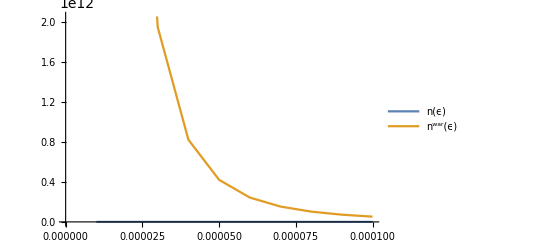

```mathematica
errors = List[];
totalerrors=List[];
nwars=List[];
(*Задаем ϵ*)
For[ϵ=0.0001, ϵ≥ 0.00001, ϵ=ϵ-0.00001,
AppendTo[errors, ϵ];
m=0;
totalerror = RINT-0;
While[totalerror > ϵ,
m=m+1;
T=Table[(2i-1)/(2m),{i,1,m},{k,1,d}];
(*Вычисляем приближенное значение интеграла*)
INT=1/m^d*((∑_(j=1)^m (T[[j,1]])^2)*∏_(k=2)^d (∑_(j=1)^m (T[[j,k]])));
totalerror=Abs[RINT-INT];
];
AppendTo[totalerrors,m^d];
AppendTo[nwars, N[1/(1+1/d)^d*(1/(2ϵ))^d]];
];
Print["Минимальное n(",errors[[1]],") = ", N[totalerrors[[1]]]];
LP1=Table[{errors[[i]],totalerrors[[i]]},{i,1,Length[errors]}];
LP2=Table[{errors[[i]],nwars[[i]]},{i,1,Length[errors]}];
ListLinePlot[{LP1,LP2},PlotLegends->{"n(ϵ)","n^war(ϵ)"}]
```